```mathematica
zippeddata = {0.3333333333333333,0.3333333333333333,0.34,0.42333333333333334,0.5433333333333333,0.7333333333333333,0.72,0.91,0.9,0.9166666666666667,0.38333333333333336,0.7266666666666667,0.8166666666666667,0.91,0.9166666666666666,0.97,0.9666666666666667,0.9833333333333333,0.9966666666666667,0.98,0.6833333333333333,0.7966666666666666,0.9233333333333333,0.93,0.97,0.9933333333333333,0.9933333333333333,0.99,0.99,0.9933333333333333};
grayscaledata = {0.3433333333333333,0.5866666666666667,0.7233333333333334,0.8533333333333334,0.87,0.8966666666666666,0.9233333333333333,0.9366666666666666,0.9433333333333334,0.95,0.6633333333333333,0.69,0.8166666666666667,0.8566666666666667,0.8833333333333333,0.9066666666666666,0.9233333333333333,0.9333333333333333,0.95,0.9566666666666667,0.6933333333333334,0.82,0.8833333333333333,0.89,0.93,0.9433333333333334,0.9533333333333334,0.9566666666666667,0.9566666666666667,0.9633333333333334};
avgdata = {0.3333333333333333,0.3466666666666667,0.33666666666666667,0.38333333333333336,0.45666666666666667,0.49,0.5033333333333333,0.5266666666666666,0.5433333333333333,0.55,0.47333333333333333,0.33666666666666667,0.4166666666666667,0.5233333333333333,0.56,0.5866666666666667,0.5933333333333334,0.5866666666666667,0.5833333333333334,0.5866666666666667,0.3566666666666667,0.4,0.4866666666666667,0.52,0.53,0.5433333333333333,0.5466666666666666,0.5533333333333333,0.5733333333333334,0.5733333333333334}
```

{0.333333,0.346667,0.336667,0.383333,0.456667,0.49,0.503333,0.526667,0.543333,0.55,0.473333,0.336667,0.416667,0.523333,0.56,0.586667,0.593333,0.586667,0.583333,0.586667,0.356667,0.4,0.486667,0.52,0.53,0.543333,0.546667,0.553333,0.573333,0.573333}

```mathematica
getplots[data_]:=Partition[data, 10] * 100
getplots@zippeddata
```

{{33.3333,33.3333,34.,42.3333,54.3333,73.3333,72.,91.,90.,91.6667},{38.3333,72.6667,81.6667,91.,91.6667,97.,96.6667,98.3333,99.6667,98.},{68.3333,79.6667,92.3333,93.,97.,99.3333,99.3333,99.,99.,99.3333}}

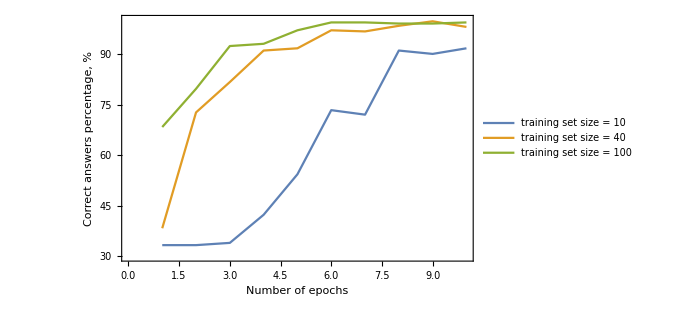

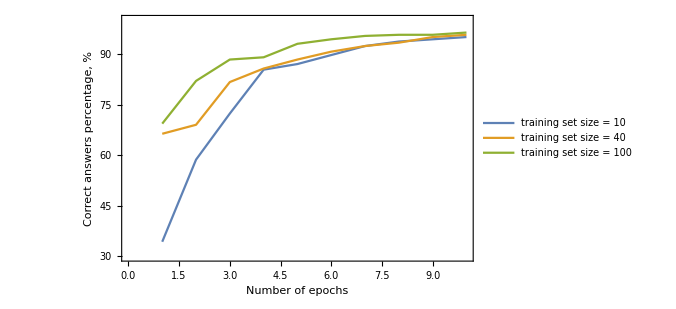

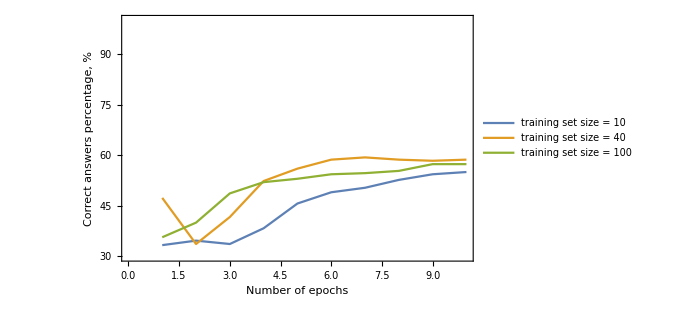

```mathematica
zipplot = ListPlot[ getplots[zippeddata], Joined->True, 
Frame-> True,
PlotLegends-> Placed[{"training set size = 10", "training set size = 40", "training set size = 100"}, Below],
FrameLabel->{"Number of epochs", "Correct answers percentage, %"},
PlotStyle->Thick,
RotateLabel->True,
ImageSize->500,
PlotRange->{{0,10}, {30, 100}}
]

gsplot =  ListPlot[ getplots[grayscaledata], Joined->True, 
Frame-> True,
PlotLegends-> Placed[{"training set size = 10", "training set size = 40", "training set size = 100"}, Below],
FrameLabel->{"Number of epochs", "Correct answers percentage, %"},
RotateLabel->True,
ImageSize->500,
PlotRange->{{0,10}, {30, 100}}
]


gsplot =  ListPlot[ getplots[avgdata], Joined->True, 
Frame-> True,
PlotLegends-> Placed[{"training set size = 10", "training set size = 40", "training set size = 100"}, Below],
FrameLabel->{"Number of epochs", "Correct answers percentage, %"},
RotateLabel->True,
ImageSize->500,
PlotRange->{{0,10}, {30, 100}}
]
```